```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/SLattice/math"];
```

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)//Simplify
```

(m^2 x^4)/(96 π^2)

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}//N
```

5.34311×10^-9

```mathematica
Sqrt[4 53+2]//N
```

14.6287

```mathematica
L=17;
```

```mathematica
dNdataTM=Import["chaotic_dN.dat"]//Flatten;
NdataYM1=Import["Ncl_lattice_RK4_1.dat"]//Flatten;
(*NdataYM2=Import["Ncl_lattice_RK4_2.dat"]//Flatten;
NdataYM3=Import["Ncl_lattice_RK4_3.dat"]//Flatten;
NdataYM4=Import["Ncl_lattice_RK4_4.dat"]//Flatten;
NdataYM5=Import["Ncl_lattice_RK4_5.dat"]//Flatten;
NdataYM6=Import["Ncl_lattice_RK4_6.dat"]//Flatten;
*)dNdataYM7=Import["dN_data_test.dat"]//Flatten;
```

```mathematica
Variance[dNdataTM]
Variance[NdataYM1]
Variance[dNdataYM7]
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)Log[L]/.{x->15,m->10^-5}//N
```

1.33038×10^-8

8.74566×10^-9

2.73535×10^-8

1.51382×10^-8

```mathematica
dNmapTM=Flatten[Table[{x,y,z,dNdataTM[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];dNmapYM1=Flatten[Table[{x,y,z,NdataYM1[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[NdataYM1]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
(*dNmap2=Flatten[Table[{x,y,z,Ndata2[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata2]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap3=Flatten[Table[{x,y,z,Ndata3[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata3]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap4=Flatten[Table[{x,y,z,Ndata4[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata4]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap5=Flatten[Table[{x,y,z,Ndata5[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata5]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
dNmap6=Flatten[Table[{x,y,z,Ndata6[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[Ndata6]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];*)
dNmapYM7=Flatten[Table[{x,y,z,dNdataYM7[[L^2(z+(L-1)/2)+L(y+(L-1)/2)+(x+(L+1)/2)]]-Mean[dNdataYM7]},{x,-(L-1)/2,(L-1)/2},{y,-(L-1)/2,(L-1)/2},{z,-(L-1)/2,(L-1)/2}],2];
```

```mathematica
ListDensityPlot3D[dNmapTM]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmapYM1]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[dNmapYM7]
```

-Graphics3D-

```mathematica
dNkTM[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmapTM[[i,1]];yy=dNmapTM[[i,2]];zz=dNmapTM[[i,3]];
dNmapTM[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmapTM]}];
dNkYM1[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmapYM1[[i,1]];yy=dNmapYM1[[i,2]];zz=dNmapYM1[[i,3]];
dNmapYM1[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmapYM1]}];
(*dNk2[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap2[[i,1]];yy=dNmap2[[i,2]];zz=dNmap2[[i,3]];
dNmap2[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap2]}];
dNk3[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap3[[i,1]];yy=dNmap3[[i,2]];zz=dNmap3[[i,3]];
dNmap3[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap3]}];
dNk4[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap4[[i,1]];yy=dNmap4[[i,2]];zz=dNmap4[[i,3]];
dNmap4[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap4]}];
dNk5[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap5[[i,1]];yy=dNmap5[[i,2]];zz=dNmap5[[i,3]];
dNmap5[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap5]}];
dNk6[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap6[[i,1]];yy=dNmap6[[i,2]];zz=dNmap6[[i,3]];
dNmap6[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap6]}];*)
dNkYM7[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmapYM7[[i,1]];yy=dNmapYM7[[i,2]];zz=dNmapYM7[[i,3]];
dNmapYM7[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmapYM7]}];
```

```mathematica
kmax=L-1;
c=10^-2;
```

```mathematica
PkdataTM[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNkTM[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
PkdataYM1[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNkYM1[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
(*Pkdata2[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk2[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata3[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk3[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata4[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk4[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata5[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk5[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
Pkdata6[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNk6[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]*)
PkdataYM7[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Abs[dNkYM7[kx,ky,kz]]^2,None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
```

```mathematica
PkListTM=Select[ParallelTable[Pkdatas=PkdataTM[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkListYM1=Select[ParallelTable[Pkdatas=PkdataYM1[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
(*PkList2=Select[ParallelTable[Pkdatas=Pkdata2[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList3=Select[ParallelTable[Pkdatas=Pkdata3[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList4=Select[ParallelTable[Pkdatas=Pkdata4[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList5=Select[ParallelTable[Pkdatas=Pkdata5[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
PkList6=Select[ParallelTable[Pkdatas=Pkdata6[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming*)
PkListYM7=Select[ParallelTable[Pkdatas=PkdataYM7[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
```

{26.6996,Null}

{24.4299,Null}

{25.8483,Null}

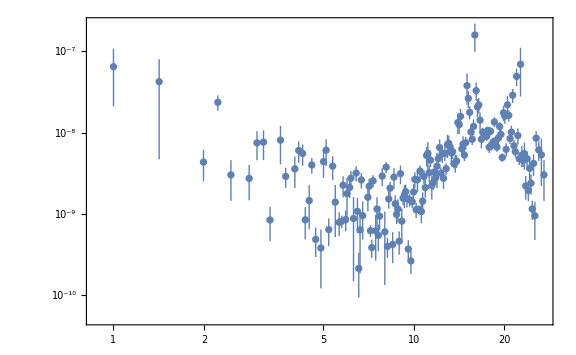

```mathematica
ListLogLogPlot[PkListTM,GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

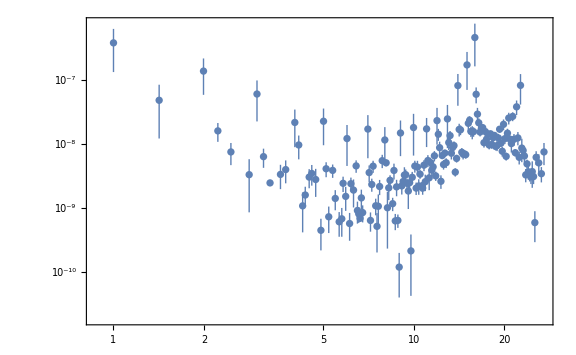

```mathematica
ListLogLogPlot[PkListYM7,GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

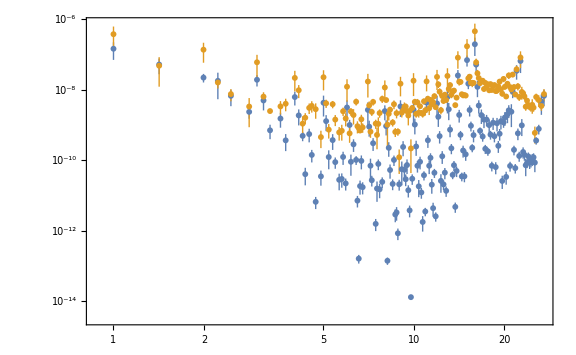

```mathematica
ListLogLogPlot[{(*PkList,*)PkListYM1(*,PkList2,PkList3,PkList4,PkList5,PkList6*),PkListYM7},GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

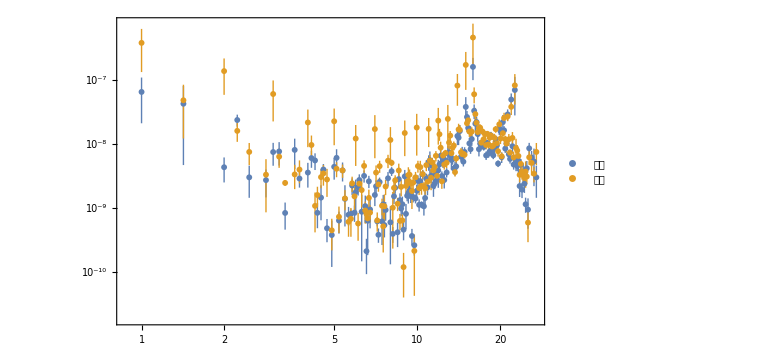

```mathematica
ListLogLogPlot[{PkListTM,(*PkList1*)(*,PkList2,PkList3,PkList4,PkList5,PkList6*)PkListYM7},GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False,PlotLegends->Placed[PointLegend[{"村田","水口"},LabelStyle->Directive[Black,Large,FontFamily->"Hiragino Sans"]],{0.2,0.2}]]
```

```mathematica
Pkdatas=PkdataYM7[4];
If[Length[Pkdatas]>1,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3),None]
```

2.16298×10^-8±1.27076×10^-8

```mathematica
PkListWOe=Select[ParallelTable[Pkdatas=Pkdata[E^lnk];If[Length[Pkdatas]>1,Total[Pkdatas]/(c L^3),None],{lnk,0,Log[Sqrt[3]kmax],c}],Positive];//AbsoluteTiming
```

{29.0663,Null}

```mathematica
c Total[PkListWOe]
Variance[dNdata]
```

1.29302×10^-8

1.33038×10^-8

```mathematica
Cxy[x_]:=Sin[x]/x/;x>0
Cxy[x_]:=1/;x==0
```

```mathematica
L=17;
kmax=L-1;
c=10^-2;
ksigmas=(2π)/L 5;
```

```mathematica
Pxi[kx_,ky_,kz_]=Sum[Cxy[ksigmas Sqrt[rx^2+ry^2+rz^2]]Exp[-I (2π)/L(kx rx+ky ry+kz rz)](*1/(c L^3)*)//N,{rx,0,L-1},{ry,0,L-1},{rz,0,L-1}]//Re;
```

```mathematica
Pxi[10,0,0]
```

0.630791

```mathematica
Pxidata[k_]:=Select[Flatten[Table[If[(k-(c k)/2)^2<=kx^2+ky^2+kz^2<(k+(c k)/2)^2,Pxi[kx,ky,kz],None],{kx,0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Abs[#]>0&]
```

```mathematica
PxiList=Select[ParallelTable[Pxidatas=Pxidata[E^lnk];If[Length[Pxidatas]>1,{E^lnk,Total[Pxidatas]/(c L^3)±1/(c L^3)Sqrt[Length[Pxidatas]]StandardDeviation[Pxidatas]},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
```

{8.27407,Null}

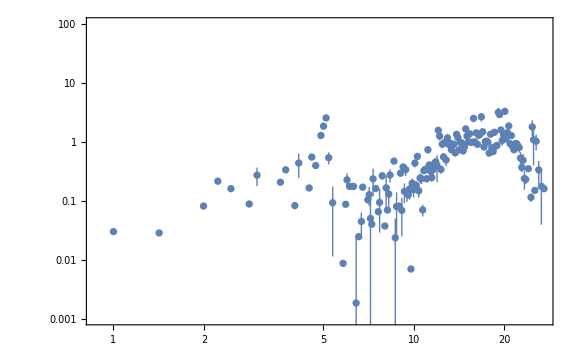

```mathematica
ListLogLogPlot[PxiList,Joined->False,PlotRange->{10^-3,10^2}]
```

```mathematica
PxiListWOe=Select[ParallelTable[Pxidatas=Pxidata[E^lnk];If[Length[Pxidatas]>1,Total[Pxidatas]/(c L^3),None],{lnk,0,Log[Sqrt[3]kmax],c}],Positive];//AbsoluteTiming
```

{8.28675,Null}

```mathematica
c Total[PxiListWOe]
```

1.0195